## Free droplet

```mathematica
Joutleft=(Diff ⅇ^(R/lmin+x0/lplus) Jin (lmin+lplus)+c0out (ⅇ^(R/l)-ⅇ^(x0/l)) (Diff+lmin v) (Diff-lplus v))/(ⅇ^(x0/l) lplus (Diff+lmin v)+ⅇ^(R/l) lmin (Diff-lplus v))/.{lin->(linplus*linmin)/(linplus+linmin),l->(lplus*lmin)/(lplus+lmin)}/.{Diff->d}/.{linplus->2*d/(Sqrt[4*d*k+v^2]+v),linmin->2*d/(Sqrt[4*d*k+v^2]-v),lplus->2*d/(Sqrt[4*d*a+v^2]+v),lmin->2*d/(Sqrt[4*d*a+v^2]-v)};
Joutright=(c0out (ⅇ^(L/l)-ⅇ^((R+x0)/l)) (Diff+lmin v) (Diff-lplus v))/(ⅇ^((R+x0)/l) lplus (Diff+lmin v)+ⅇ^(L/l) lmin (Diff-lplus v))/.{lin->(linplus*linmin)/(linplus+linmin),l->(lplus*lmin)/(lplus+lmin)}/.{Diff->d}/.{linplus->2*d/(Sqrt[4*d*k+v^2]+v),linmin->2*d/(Sqrt[4*d*k+v^2]-v),lplus->2*d/(Sqrt[4*d*a+v^2]+v),lmin->2*d/(Sqrt[4*d*a+v^2]-v)};
Jrad = -2 c0in Diff/lin Csch[ R/lin] Sinh[R/linmin] Sinh[R/linplus]/.{lin->(linplus*linmin)/(linplus+linmin),l->(lplus*lmin)/(lplus+lmin)}/.{Diff->d}/.{linplus->2*d/(Sqrt[4*d*k+v^2]+v),linmin->2*d/(Sqrt[4*d*k+v^2]-v),lplus->2*d/(Sqrt[4*d*a+v^2]+v),lmin->2*d/(Sqrt[4*d*a+v^2]-v)};
Jpos=1/(linmin linplus)2 c0in Csch[ R/lin] (linmin (-Diff+linplus v) Cosh[R/linplus] Sinh[R/linmin]+linplus (Diff+linmin v) Cosh[R/linmin] Sinh[R/linplus])/.{Diff->d}/.{lin->(linplus*linmin)/(linplus+linmin),l->(lplus*lmin)/(lplus+lmin)}/.{linplus->2*d/(Sqrt[4*d*k+v^2]+v),linmin->2*d/(Sqrt[4*d*k+v^2]-v),lplus->2*d/(Sqrt[4*d*a+v^2]+v),lmin->2*d/(Sqrt[4*d*a+v^2]-v)};
cin=c0in ⅇ^(-x/linmin-x0/linplus) Csch[(1/linmin+1/linplus) R] (ⅇ^((1/linmin+1/linplus) x) Sinh[R/linmin]+ⅇ^((1/linmin+1/linplus) x0) Sinh[R/linplus])/.{Diff->d}/.{lin->(linplus*linmin)/(linplus+linmin),l->(lplus*lmin)/(lplus+lmin)}/.{linplus->2*d/(Sqrt[4*d*k+v^2]+v),linmin->2*d/(Sqrt[4*d*k+v^2]-v),lplus->2*d/(Sqrt[4*d*a+v^2]+v),lmin->2*d/(Sqrt[4*d*a+v^2]-v)};
coutleft=(ⅇ^(-x/lmin) (-(ⅇ^(((lmin+lplus) (R+x))/(lmin lplus))-ⅇ^((1/lmin+1/lplus) x0)) Jin lmin lplus+c0out ⅇ^(R/lplus+x0/lmin) (ⅇ^((1/lmin+1/lplus) x) lplus (Diff+lmin v)+lmin (Diff-lplus v))))/(ⅇ^((1/lmin+1/lplus) x0) lplus (Diff+lmin v)+ⅇ^((1/lmin+1/lplus) R) lmin (Diff-lplus v))/.{lin->(linplus*linmin)/(linplus+linmin),l->(lplus*lmin)/(lplus+lmin)}/.{Diff->d}/.{linplus->2*d/(Sqrt[4*d*k+v^2]+v),linmin->2*d/(Sqrt[4*d*k+v^2]-v),lplus->2*d/(Sqrt[4*d*a+v^2]+v),lmin->2*d/(Sqrt[4*d*a+v^2]-v)};
coutright=(c0out ⅇ^((R-x+x0)/lmin) (ⅇ^((1/lmin+1/lplus) x) lplus (Diff+lmin v)+ⅇ^(L (1/lmin+1/lplus)) lmin (Diff-lplus v)))/(ⅇ^(((lmin+lplus) (R+x0))/(lmin lplus)) lplus (Diff+lmin v)+ⅇ^(L (1/lmin+1/lplus)) lmin (Diff-lplus v))/.{lin->(linplus*linmin)/(linplus+linmin),l->(lplus*lmin)/(lplus+lmin)}/.{Diff->d}/.{linplus->2*d/(Sqrt[4*d*k+v^2]+v),linmin->2*d/(Sqrt[4*d*k+v^2]-v),lplus->2*d/(Sqrt[4*d*a+v^2]+v),lmin->2*d/(Sqrt[4*d*a+v^2]-v)};
cmin:=1/linmin c0in ⅇ^((linplus (Log[linmin]-Log[linplus]+Log[Sinh[R/linmin]]-Log[Sinh[R/linplus]]))/(linmin+linplus)) (linmin+linplus) Csch[(1/linmin+1/linplus) R] Sinh[R/linplus]/.{Diff->d}/.{linplus->2*d/(Sqrt[4*d*k+v^2]+v),linmin->2*d/(Sqrt[4*d*k+v^2]-v),lplus->2*d/(Sqrt[4*d*a+v^2]+v),lmin->2*d/(Sqrt[4*d*a+v^2]-v)};
```

```mathematica
dRdt=Jrad+(Joutleft-Joutright);
dxdt=Jpos-(Joutleft+Joutright);
```

### No decay

```mathematica
params={d->1.0,k->0.1,a->0.0,c0out->0.1,c0in->0.9}
```

{d→1.,k→0.1,a→0.,c0out→0.1,c0in→0.9}

```mathematica
FullSimplify[dRdt/.a->0,v>0]
```

Jin+c0in √(4 d k+v^2) (Cosh[(R v)/d]-Cosh[(R √(4 d k+v^2))/d]) Csch[(R √(4 d k+v^2))/d]

```mathematica
Rstable[J_,vin_,paramsin_]:=FindRoot[Jin+c0in √(4 d k+v^2) (Cosh[(R v)/d]-Cosh[(R √(4 d k+v^2))/d]) Csch[(R √(4 d k+v^2))/d]/.paramsin/.{Jin->J,v->vin},{R,10^-5}]
```

```mathematica
FullSimplify[dxdt/.a->0,v>0]
```

-Jin+c0in v+c0in √(4 d k+v^2) Csch[(R √(4 d k+v^2))/d] Sinh[(R v)/d]

```mathematica
Xstable[J_,vin_,paramsin_]:=-Jin+c0in v+c0in √(4 d k+v^2) Csch[(R √(4 d k+v^2))/d] Sinh[(R v)/d]/.Rstable[J,vin,paramsin]/.paramsin/.{Jin->J,v->vin}
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-Graphics-

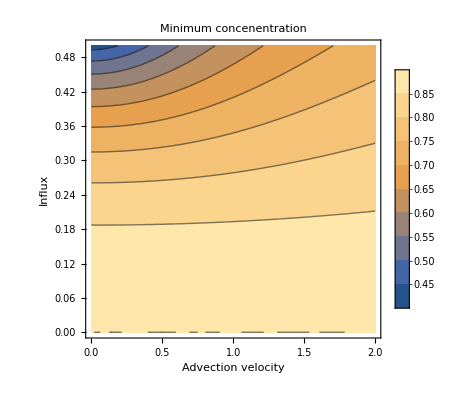

```mathematica
p1=ContourPlot[(R/.Rstable[J,v,params]),{v,0,2},{J,0,0.5},Mesh->{{0}},MeshFunctions->{Xstable[#2,#1,params]&},
PlotLabel->"Stable droplet radius",FrameLabel->{"Advection velocity","Influx"},PlotLegends->Automatic, BaseStyle->{FontFamily->"Helvetica",FontSize->12}];
p2 = ContourPlot[cmin/.params/.Rstable[J,v,params],{v,0,2},{J,0,0.5}, PlotLabel->"Minimum concentration",FrameLabel->{"Advection velocity","Influx"},PlotLegends->Automatic, BaseStyle->{FontFamily->"Helvetica",FontSize->12}];
gg = GraphicsGrid[{{p1, p2}}, ImageSize->Large]
```

1.49021

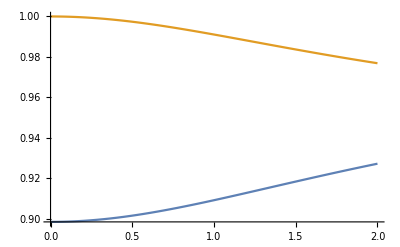

```mathematica
Jplot=0.25;
normR=R/.Rstable[Jplot,0,params]/.J->Jplot
Plot[{(cmin/c0in/.params/.Rstable[Jplot,v,params]/.J->Jplot),(R/.Rstable[Jplot,v,params]/.J->Jplot)/normR},{v,0,2}]
```

```mathematica
FullSimplify
```

-2 (c0in dr k)+2 c0in k r+O[r]^2